```mathematica
thisfolder=NotebookDirectory[];
```

### get the transit duration

```mathematica
fitsfolder=StringReplace[thisfolder,"superfold"->"fits"];
ttvpost1=Import[StringJoin[fitsfolder,"TTVplan1-post_equal_weights.dat"],"Table"];
ttvpost2=Import[StringJoin[fitsfolder,"TTVplan2-post_equal_weights.dat"],"Table"];
ttvpost3=Import[StringJoin[fitsfolder,"TTVplan3-post_equal_weights.dat"],"Table"];
```

```mathematica
Grv=6.674*10^(-11);
aR[ρstar_,Pdays_]:=(((ρstar*Grv)/(3Pi)) (Pdays*86400)^2)^(1/3);
T14[ρstar_,Pdays_,p_,b_]:=(Pdays*86400)/Pi  ArcSin[√(((1+p)^2-b^2)/(aR[ρstar,Pdays]^2-b^2))];
```

```mathematica
"segment 1";
ptab1=ttvpost1[[All,1]];
rhostartab1=ttvpost1[[All,2]];
btab1=ttvpost1[[All,3]];
Pdaystab1=ttvpost1[[All,4]];
T14tab1=Table[Re[T14[rhostartab1[[i]],Pdaystab1[[i]],ptab1[[i]],btab1[[i]]]]/86400,{i,1,Length[ttvpost1]}];
Ttab1=Table[Re[T14[rhostartab1[[i]],Pdaystab1[[i]],0,btab1[[i]]]]/86400,{i,1,Length[ttvpost1]}];
"segment 2";
ptab2=ttvpost2[[All,1]];
rhostartab2=ttvpost2[[All,2]];
btab2=ttvpost2[[All,3]];
Pdaystab2=ttvpost2[[All,4]];
T14tab2=Table[Re[T14[rhostartab2[[i]],Pdaystab2[[i]],ptab2[[i]],btab2[[i]]]]/86400,{i,1,Length[ttvpost2]}];
Ttab2=Table[Re[T14[rhostartab2[[i]],Pdaystab2[[i]],0,btab2[[i]]]]/86400,{i,1,Length[ttvpost2]}];
"segment 3";
ptab3=ttvpost3[[All,1]];
rhostartab3=ttvpost3[[All,2]];
btab3=ttvpost3[[All,3]];
Pdaystab3=ttvpost3[[All,4]];
T14tab3=Table[Re[T14[rhostartab3[[i]],Pdaystab3[[i]],ptab3[[i]],btab3[[i]]]]/86400,{i,1,Length[ttvpost3]}];
Ttab3=Table[Re[T14[rhostartab3[[i]],Pdaystab3[[i]],0,btab3[[i]]]]/86400,{i,1,Length[ttvpost3]}];
```

```mathematica
star=Import[StringReplace[NotebookDirectory[],"fits/"->"isochrones/post.dat"],"Table"];
Rstartab=star[[All,5]];
RSun=6.957*10^8;REarth=6783100;
MEarth=5.9722*10^24;MSun=1.98847*10^30;
```

```mathematica
SeedRandom[42]
ptabJ=Join[ptab1,ptab2,ptab3];
Rptab=Table[ptabJ[[i]]* Rstartab[[i]] RSun/REarth,{i,1,Min[Length[Rstartab],Length[ptabJ]]}];
```

RandomGeneratorState[…]

```mathematica
Export[StringJoin[NotebookDirectory[],"Rp_obs.dat"],Rptab,"Table"]
```

/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/MoonFold/KOI-1841.01/fits/Rp_obs.dat

import result from forecaster...

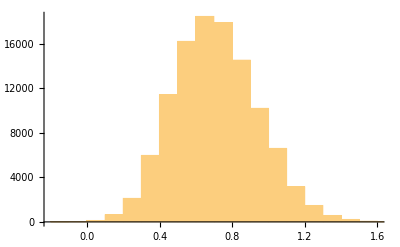

```mathematica
Mppred=Flatten[Import[StringJoin[NotebookDirectory[],"Mp_pred.dat"],"Table"]];
Histogram[Log10[Mppred]]
```

### get planet TTVs

```mathematica
bestPK=17.30310262529833;
bestθK={49.607483366616236,54971.41750821662,-0.005648176836207876,-0.0005631281637963544}
bestsinusoidK[e_]:=bestθK[[1]] e+bestθK[[2]]+bestθK[[3]] Sin[(2π e)/bestPK]+bestθK[[4]] Cos[(2π e)/bestPK];
```

{49.6075,54971.4,-0.00564818,-0.000563128}

```mathematica
linmodel[e_]:=bestθK[[1]] e+bestθK[[2]]
τglob=bestθK[[2]]
Pglob=bestθK[[1]]
```

54971.4

49.6075

```mathematica
TTVp[e_]:=bestθK[[3]] Sin[(2π e)/bestPK]+bestθK[[4]] Cos[(2π e)/bestPK]
τplanet[e_]:=linmodel[e]+TTVp[e]
TTVs[e_,Msp_]:=-TTVp[e]/Msp;
τsat[e_,Msp_]:=linmodel[e]+TTVs[e,Msp]
```

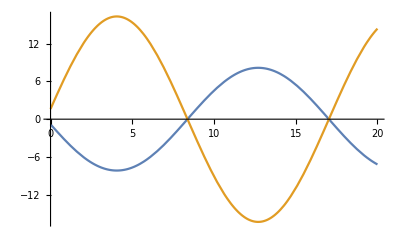

```mathematica
Plot[{1440TTVp[t],1440TTVs[t,0.5]},{t,0,20}]
```

### define brackets of when the planetary transit occurs

```mathematica
sigma=2;
integP=0.02043361111111111;
```

```mathematica
j=0;
"segment 1";
dim1=Last[Dimensions[ttvpost1]];
taupost1=ttvpost1[[All,8;;dim1-1]];
k=0;Label[kloop1];k=k+1;j=j+1;Subscript[τtab, j]=taupost1[[All,k]];Subscript[epochy, j]=Round[(Median[Subscript[τtab, j]]-τglob)/Pglob];temp=Table[{Subscript[τtab, j][[i]]-0.5T14tab1[[i]]-0.5integP,Subscript[τtab, j][[i]]+0.5T14tab1[[i]]+0.5integP},{i,1,Length[T14tab1]}];TpbracketA={Quantile[temp[[All,1]],Erfc[sigma/√2]],Median[Subscript[τtab, j]],Quantile[temp[[All,2]],Erf[sigma/√2]]};TpbracketB={τplanet[Subscript[epochy, j]]-0.5Quantile[T14tab1,Erf[sigma/√2]]-0.5integP,τplanet[Subscript[epochy, j]],τplanet[Subscript[epochy, j]]+0.5Quantile[T14tab1,Erf[sigma/√2]]+0.5integP};Subscript[TpbracketX, j]={Min[TpbracketA[[1]],TpbracketB[[1]]],Max[TpbracketA[[3]],TpbracketB[[3]]]};Subscript[TsbracketX, j]={τsat[Subscript[epochy, j],Msp]-0.5Median[Ttab1],τsat[Subscript[epochy, j],Msp]+0.5Median[Ttab1]};If[k<dim1-7-1,Goto[kloop1]];"segment 2";
dim2=Last[Dimensions[ttvpost2]];
taupost2=ttvpost2[[All,8;;dim2-1]];
k=0;Label[kloop2];k=k+1;j=j+1;Subscript[τtab, j]=taupost2[[All,k]];Subscript[epochy, j]=Round[(Median[Subscript[τtab, j]]-τglob)/Pglob];temp=Table[{Subscript[τtab, j][[i]]-0.5T14tab2[[i]]-0.5integP,Subscript[τtab, j][[i]]+0.5T14tab2[[i]]+0.5integP},{i,1,Length[T14tab2]}];TpbracketA={Quantile[temp[[All,1]],Erfc[sigma/√2]],Median[Subscript[τtab, j]],Quantile[temp[[All,2]],Erf[sigma/√2]]};TpbracketB={τplanet[Subscript[epochy, j]]-0.5Quantile[T14tab2,Erf[sigma/√2]]-0.5integP,τplanet[Subscript[epochy, j]],τplanet[Subscript[epochy, j]]+0.5Quantile[T14tab2,Erf[sigma/√2]]+0.5integP};Subscript[TpbracketX, j]={Min[TpbracketA[[1]],TpbracketB[[1]]],Max[TpbracketA[[3]],TpbracketB[[3]]]};Subscript[TsbracketX, j]={τsat[Subscript[epochy, j],Msp]-0.5Median[Ttab2],τsat[Subscript[epochy, j],Msp]+0.5Median[Ttab2]};If[k<dim2-7-1,Goto[kloop2]];"segment 3";
dim3=Last[Dimensions[ttvpost3]];
taupost3=ttvpost3[[All,8;;dim3-1]];
k=0;Label[kloop3];k=k+1;j=j+1;Subscript[τtab, j]=taupost3[[All,k]];Subscript[epochy, j]=Round[(Median[Subscript[τtab, j]]-τglob)/Pglob];temp=Table[{Subscript[τtab, j][[i]]-0.5T14tab3[[i]]-0.5integP,Subscript[τtab, j][[i]]+0.5T14tab3[[i]]+0.5integP},{i,1,Length[T14tab3]}];TpbracketA={Quantile[temp[[All,1]],Erfc[sigma/√2]],Median[Subscript[τtab, j]],Quantile[temp[[All,2]],Erf[sigma/√2]]};TpbracketB={τplanet[Subscript[epochy, j]]-0.5Quantile[T14tab3,Erf[sigma/√2]]-0.5integP,τplanet[Subscript[epochy, j]],τplanet[Subscript[epochy, j]]+0.5Quantile[T14tab3,Erf[sigma/√2]]+0.5integP};Subscript[TpbracketX, j]={Min[TpbracketA[[1]],TpbracketB[[1]]],Max[TpbracketA[[3]],TpbracketB[[3]]]};Subscript[TsbracketX, j]={τsat[Subscript[epochy, j],Msp]-0.5Median[Ttab3],τsat[Subscript[epochy, j],Msp]+0.5Median[Ttab3]};If[k<dim3-7-1,Goto[kloop3]];
```

### obtain lightcurve

```mathematica
lc=Import[StringJoin[thisfolder,"AVG_SAP.dat"],"Table"];
lc=Table[{lc[[i,1]],lc[[i,2]],lc[[i,3]],Round[(lc[[i,1]]-τglob)/Pglob]},{i,1,Length[lc]}];
uniqueepochs=Union[lc[[All,4]]]
nepochs=Length[uniqueepochs]
```

{0,1,2,3,4,5,6,7,8,9,10,11,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

28

```mathematica
<<ErrorBarPlots`
```

```mathematica
yrange={0.999,1.0005}
planetzone=Directive[Lighter[Blue],Opacity[0.2]];
MspX=0.01;
moonzone=Directive[Lighter[Red],Opacity[0.2]];
```

{0.999,1.0005}

11

12

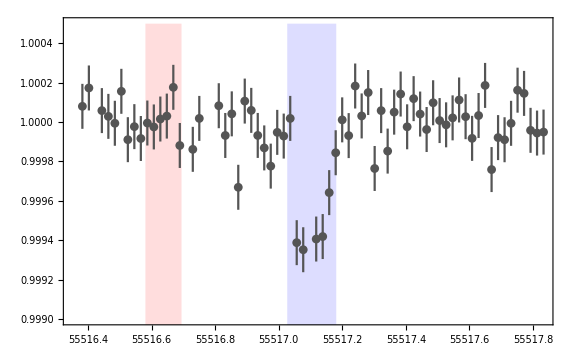

```mathematica
k=12;
thisepoch=uniqueepochs[[k]]
thisj=Select[Table[{i,Subscript[epochy, i]},{i,1,nepochs}],#[[2]]==thisepoch&][[1]][[1]]
thislc=Select[lc,#[[4]]==thisepoch&];
Show[ErrorListPlot[thislc[[All,{1,2,3}]],PlotRange->{All,yrange},Joined->False,PlotStyle->Directive[Lighter[Black],Opacity[0]],Frame->True,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},ImageSize->Large],Plot[yrange[[2]],{x,First[Subscript[TpbracketX, thisj]],Last[Subscript[TpbracketX, thisj]]},PlotStyle->None,Filling->Axis,FillingStyle->planetzone],Plot[yrange[[2]],{x,First[Subscript[TsbracketX, thisj]]/.Msp->MspX,Last[Subscript[TsbracketX, thisj]]/.Msp->MspX},PlotStyle->None,Filling->Axis,FillingStyle->moonzone],ErrorListPlot[thislc[[All,{1,2,3}]],PlotRange->{All,yrange},PlotStyle->Directive[Lighter[Black]]]]
```

### determine min allowed Msp

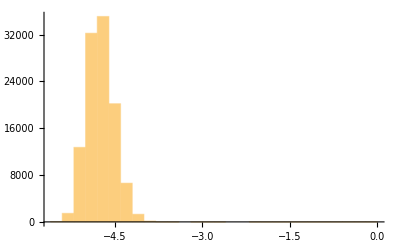

```mathematica
qdist=Table[(Mppred[[i]] MEarth)/(star[[i,4]] MSun),{i,1,Min[Length[star],Length[Mppred]]}];
Histogram[Log10[qdist]]
```

```mathematica
qrough=10*5.9722*10^24/(0.858*1.989*10^30)
Log10[qrough]
```

0.0000349955

-4.45599

```mathematica
qroughlow=Quantile[qdist,Erfc[2/√2]]
qroughhigh=Quantile[qdist,Erf[2/√2]]
```

7.81507×10^-6

0.000046269

```mathematica
TTVprough=1440 √(bestθK[[3]]^2+bestθK[[4]]^2)
```

8.1737

```mathematica
Mspmin=((fmax (qroughhigh/3)^(1/3))/((2π/Pglob)( TTVprough/1440))-1)^-1/.fmax->1
```

0.0297414

```mathematica
Mspmax=((fmin (qroughlow/3)^(1/3))/((2π/Pglob)( TTVprough/1440))-1)^-1/.fmin->(3 ((10 Median[T14tab1])/Pglob)^2)^(1/3)
```

0.747556

## LOOP IT

```mathematica
steps=100;
logMspmin=Log[Mspmin];logMspmax=Log[Mspmax];
Msplist=Table[Exp[logMspmin+(k-1)((logMspmax-logMspmin)/(steps-1))],{k,1,steps}];
```

```mathematica
tstart=AbsoluteTime[];k=0;Label[kloop];k=k+1;MspX=Msplist[[k]];"STEP 2";j=0;Label[jloop];j=j+1;thisepoch=uniqueepochs[[j]];thisj=Select[Table[{i,Subscript[epochy, i]},{i,1,nepochs}],#[[2]]==thisepoch&][[1]][[1]];thislc=Select[lc,#[[4]]==thisepoch&];TPBRACKET={First[Subscript[TpbracketX, thisj]],Last[Subscript[TpbracketX, thisj]]};TSBRACKET={First[Subscript[TsbracketX, thisj]]/.Msp->MspX,Last[Subscript[TsbracketX, thisj]]/.Msp->MspX};tempin=Select[lc,TSBRACKET[[1]]≤#[[1]]≤TSBRACKET[[2]]&];tempin=Select[tempin,!(TPBRACKET[[1]]≤#[[1]]≤TPBRACKET[[2]])&];tempout=Select[lc,TPBRACKET[[1]]-0.5Pglob≤#[[1]]≤TPBRACKET[[2]]+0.5Pglob&];tempout=Select[tempout,!(TSBRACKET[[1]]≤#[[1]]≤TSBRACKET[[2]])&];tempout=Select[tempout,!(TPBRACKET[[1]]≤#[[1]]≤TPBRACKET[[2]])&];Subscript[appendin, j]=Table[{tempin[[i,1]]-Mean[TSBRACKET],tempin[[i,2]],tempin[[i,3]]},{i,1,Length[tempin]}];Subscript[appendout, j]=Table[{tempout[[i,1]]-Mean[TSBRACKET],tempout[[i,2]],tempout[[i,3]]},{i,1,Length[tempout]}];If[j<nepochs,Goto[jloop]];"STEP 3";inside=Sort[Flatten[Table[Subscript[appendin, jj],{jj,1,nepochs}],1]];outside=Sort[Flatten[Table[Subscript[appendout, jj],{jj,1,nepochs}],1]];If[Length[inside]>0,theoryerror=√((Sum[inside[[i,3]]^-2,{i,1,Length[inside]}]^(-1/2))^2+(Sum[outside[[i,3]]^-2,{i,1,Length[outside]}]^(-1/2))^2),theoryerror=√((Sum[outside[[i,3]]^-2,{i,1,Length[outside]}]^(-1/2))^2)];If[Length[inside]>0,μin=Sum[inside[[i,2]] inside[[i,3]]^-2,{i,1,Length[inside]}]/Sum[inside[[i,3]]^-2,{i,1,Length[inside]}],μin=1];μout=Sum[outside[[i,2]] outside[[i,3]]^-2,{i,1,Length[outside]}]/Sum[outside[[i,3]]^-2,{i,1,Length[outside]}];If[Length[inside]>0,joint=Join[inside,outside],joint=outside];μjoint=Sum[joint[[i,2]] joint[[i,3]]^-2,{i,1,Length[joint]}]/Sum[joint[[i,3]]^-2,{i,1,Length[joint]}];chi2flat=Sum[((joint[[i,2]]-μjoint)/joint[[i,3]])^2,{i,1,Length[joint]}];If[Length[inside]>0,chi2best=Sum[((outside[[i,2]]-μout)/outside[[i,3]])^2,{i,1,Length[outside]}]+Sum[((inside[[i,2]]-μin)/inside[[i,3]])^2,{i,1,Length[inside]}],chi2best=chi2flat];bestdip=(μout-μin);chi2model[ppmdip_]:=Sum[((outside[[i,2]]-μout)/outside[[i,3]])^2,{i,1,Length[outside]}]+Sum[((inside[[i,2]]-(μout-ppmdip))/inside[[i,3]])^2,{i,1,Length[inside]}];diplimit1σ=10^6Max[Last[Last[Last[NMinimize[{(chi2model[x]-(chi2flat+1))^2,x>bestdip},{x,0,10*10^6 theoryerror},Method->"NelderMead"]]]],0];diplimit2σ=10^6Max[Last[Last[Last[NMinimize[{(chi2model[x]-(chi2flat+4))^2,x>bestdip},{x,0,10*10^6 theoryerror},Method->"NelderMead"]]]],0];diplimit3σ=10^6Max[Last[Last[Last[NMinimize[{(chi2model[x]-(chi2flat+9))^2,x>bestdip},{x,0,10*10^6 theoryerror},Method->"NelderMead"]]]],0];Subscript[α, k]={MspX,10^6(μout-μin),bestdip,10^6 theoryerror,chi2flat-chi2best,diplimit1σ,diplimit2σ,diplimit3σ,Length[inside]};If[k<Length[Msplist],Goto[kloop]];
tend=AbsoluteTime[];
tend-tstart
```

63.204181

```mathematica
"{Msp,simple depth [ppm],fitted depth [ppm],theory error [ppm],Δχ^2,δ1,δ2,δ3}";
```

```mathematica
result=Select[Table[{Log10[Subscript[α, kk][[1]]],Subscript[α, kk][[2]],Subscript[α, kk][[3]],Subscript[α, kk][[4]],Subscript[α, kk][[5]],Subscript[α, kk][[6]],Subscript[α, kk][[7]],Subscript[α, kk][[8]],Subscript[α, kk][[9]]},{kk,1,Length[Msplist]}],#[[9]]>0&];
```

```mathematica
TTVp==asp (Msp/(1+Msp))Pp/(2π ap)
TTVp==asp/Rp (Msp/(1+Msp))(Pp Rp)/(2π ap)
TTVp==asp/Rp (Msp/(1+Msp))(Pp Rstar)/(2π ap)Rp/Rstar
TTVp==(asp/Rp) (Msp/(1+Msp))Pp/(2π aR)p
```

```mathematica
TTVprough/1440==(asp/Rp) (Msp/(1+Msp))0.0014662708980739765
682.0022148114324 TTVprough/1440((Msp+1)/Msp)==(asp/Rp)
```

```mathematica
asppconversion[Msp_]:=682.0022148114324 TTVprough/1440((Msp+1)/Msp);
xticks0={0.03,0.04,0.06,0.08,0.10,0.20,0.30,0.4};
xticks=Table[{Log10[xticks0[[i]]],ToString[xticks0[[i]]]},{i,1,Length[xticks0]}];
xticks2=Table[{Log10[xticks0[[i]]],ToString[Round[asppconversion[xticks0[[i]]],1]]},{i,1,Length[xticks0]}]
{{-1.5228787452803376,"0.03"},{-1.3979400086720375,"0.04"},{-1.3010299956639813,"0.05"},{-1.2218487496163564,"0.06"},{-1.154901959985743,"0.07"},{-1.0969100130080565,"0.08"},{-1.0457574905606752,"0.09"},{-1.,"0.1"},{-0.6989700043360187,"0.2"},{-0.5228787452803376,"0.3"}}
{{-1.5228787452803376,"120.4"},{-1.3979400086720375,"91.2"},{-1.3010299956639813,"73.7"},{-1.2218487496163564,"62."},{-1.154901959985743,"53.6"},{-1.0969100130080565,"47.4"},{-1.0457574905606752,"42.5"},{-1.,"38.6"},{-0.6989700043360187,"21."},{-0.5228787452803376,"15.2"}};
```

{{-1.52288,133},{-1.39794,101},{-1.22185,68},{-1.09691,52},{-1.,43},{-0.69897,23},{-0.522879,17},{-0.39794,14}}

{{-1.52288,0.03},{-1.39794,0.04},{-1.30103,0.05},{-1.22185,0.06},{-1.1549,0.07},{-1.09691,0.08},{-1.04576,0.09},{-1.,0.1},{-0.69897,0.2},{-0.522879,0.3}}

```mathematica
asppconversion[0.35]
```

14.9316

```mathematica
aticks={15,20,30,40,50,75,100,125};
xticks2=Table[{Log10[Last[NSolve[aticks[[i]]==asppconversion[Msp],Msp][[1,1]]]],ToString[aticks[[i]]]},{i,1,Length[aticks]}];
```

```mathematica
yticks0={-100,-50,0,50,100,150,200,250,300};
yticks=Table[{yticks0[[i]],ToString[yticks0[[i]]]},{i,1,Length[yticks0]}];
Rmedian=Median[Rstartab];
Rvals={{-1,"-R_♁"},{-0.7,"-0.7R_♁"},{-0.533,"-R_♂"},{0,"0"},{0.533,"R_♂"},{0.7,"0.7R_♁"},{1,"R_♁"},{1.5,"1.5R_♁"}};
yticks2=Table[{Sign[Rvals[[i,1]]] 10^6(Rvals[[i,1]] REarth/(Rmedian RSun))^2,Rvals[[i,2]]},{i,1,Length[Rvals]}]
```

{{-141.519,-R_♁},{-69.3443,-0.7R_♁},{-40.204,-R_♂},{0.,0},{40.204,R_♂},{69.3443,0.7R_♁},{141.519,R_♁},{318.418,1.5R_♁}}

```mathematica
region0=Table[{result[[i,1]],result[[i,2]]},{i,1,Length[result]}];
region1d=Table[{result[[i,1]],result[[i,2]]-result[[i,4]]},{i,1,Length[result]}];
region1u=Table[{result[[i,1]],result[[i,2]]+result[[i,4]]},{i,1,Length[result]}];
plotty=Show[ListPlot[{region1d,region1u},Joined->True,Filling->{1->{2}},ImageSize->{800,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},AspectRatio->0.5,PlotRange->{{Log10[Mspmin],Log10[0.4]},{-120,320}},Frame->True,GridLines->{{},{{10^6((0.533REarth)/(Rmedian RSun))^2,Directive[Black,Thickness[0.003],Dashing[0.015]]}}},FrameLabel->{{"δ_sat [ppm]",""},{"satellite-to-planet mass ratio, M_SP","estimated separation, a_SP/R_P"}},FrameTicks->{{yticks,yticks2},{xticks,xticks2}},PlotStyle->ColorData["CherryTones"][0.4],FillingStyle->Directive[ColorData["CherryTones"][0.4],Opacity[0.25]]],ListPlot[result[[All,{1,7}]],Joined->True,PlotStyle->Directive[Lighter[Black],Thickness[0.002]],Filling->320,FillingStyle->Directive[HatchFilling[45],Opacity[0.3]]],ListPlot[result[[All,{1,7}]],Joined->True,PlotStyle->Directive[Lighter[Black],Thickness[0.002]],Filling->320,FillingStyle->Directive[HatchFilling[-45],Opacity[0.3]]]]
```

-Graphics-

```mathematica
c1=1.008;t1=2.04;s1=0.279;t2=131.6;s2=0.589;t3=26637.2;s3=-0.044;s4=0.881;
c2=c1*t1^(s1-s2);c3=c2*t2^(s2-s3);c4=c3*t3^(s3-s4);
t0=0.000335;t4=289680;
Rpred[M_]:=Piecewise[{{c1*M^s1,t0<M≤t1},{c2*M^s2,t1<M≤t2},{c3*M^s3,t2<M≤t3},{c4*M^s4,t3<M≤t4}}];
```

```mathematica
Rsatpred=Table[{10^result[[i,1]],Rpred[(10^result[[i,1]])*Median[Mppred]]},{i,1,Length[result]}];
```

```mathematica
Rsatpred=Table[{Log10[Rsatpred[[i,1]]],Rsatpred[[i,2]],10^6((Rsatpred[[i,2]] REarth)/(Rmedian RSun))^2},{i,1,Length[result]}];
```

```mathematica
finalplot=Show[plotty,ListPlot[Rsatpred[[All,{1,3}]],Joined->True,PlotStyle->Directive[Thickness[0.0025],ColorData["CherryTones"][0.4]]]]
Export[StringJoin[NotebookDirectory[],"KOI1841_plot.pdf"],finalplot]
```

-Graphics-

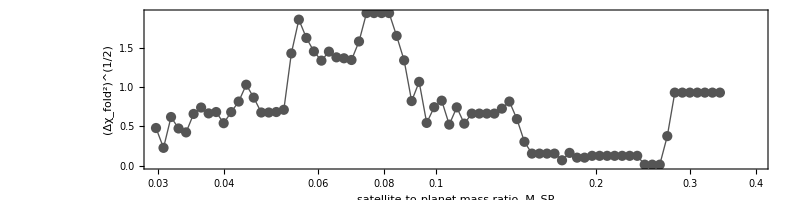

```mathematica
tempy=Table[{result[[i,1]],√result[[i,5]]},{i,1,Length[result]}];
ListPlot[{tempy,tempy},Joined->{False,True},ImageSize->{800,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},AspectRatio->0.25,PlotRange->{{Log10[Mspmin],Log10[0.4]},All},Frame->True,FrameLabel->{{"(Δχ_fold^2)^(1/2)",""},{"satellite-to-planet mass ratio, M_SP","estimated separation, a_SP/R_P"}},FrameTicks->{{Automatic,Automatic},{xticks,xticks2}},PlotStyle->{Directive[Lighter[Black],Thickness[0.005]],Directive[Lighter[Black],Thickness[0.0012]]}]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"chi2_plot.pdf"],%]
```

### plot it

```mathematica
Reverse[Sort[Select[result[[All,{5,1}]],#[[2]]<0.2&]]][[1]]
```

{3.75501,-1.1306}

```mathematica
MspX=10^(-1.130599695719224);
"STEP 2";j=0;Label[jloop];j=j+1;thisepoch=uniqueepochs[[j]];thisj=Select[Table[{i,Subscript[epochy, i]},{i,1,nepochs}],#[[2]]==thisepoch&][[1]][[1]];thislc=Select[lc,#[[4]]==thisepoch&];TPBRACKET={First[Subscript[TpbracketX, thisj]],Last[Subscript[TpbracketX, thisj]]};TSBRACKET={First[Subscript[TsbracketX, thisj]]/.Msp->MspX,Last[Subscript[TsbracketX, thisj]]/.Msp->MspX};tempin=Select[lc,TSBRACKET[[1]]≤#[[1]]≤TSBRACKET[[2]]&];tempin=Select[tempin,!(TPBRACKET[[1]]≤#[[1]]≤TPBRACKET[[2]])&];tempout=Select[lc,TPBRACKET[[1]]-0.5Pglob≤#[[1]]≤TPBRACKET[[2]]+0.5Pglob&];tempout=Select[tempout,!(TSBRACKET[[1]]≤#[[1]]≤TSBRACKET[[2]])&];tempout=Select[tempout,!(TPBRACKET[[1]]≤#[[1]]≤TPBRACKET[[2]])&];Subscript[appendin, j]=Table[{tempin[[i,1]]-Mean[TSBRACKET],tempin[[i,2]],tempin[[i,3]]},{i,1,Length[tempin]}];Subscript[appendout, j]=Table[{tempout[[i,1]]-Mean[TSBRACKET],tempout[[i,2]],tempout[[i,3]]},{i,1,Length[tempout]}];If[j<nepochs,Goto[jloop]];"STEP 3";inside=Sort[Flatten[Table[Subscript[appendin, jj],{jj,1,nepochs}],1]];outside=Sort[Flatten[Table[Subscript[appendout, jj],{jj,1,nepochs}],1]];If[Length[inside]>0,theoryerror=√((Sum[inside[[i,3]]^-2,{i,1,Length[inside]}]^(-1/2))^2+(Sum[outside[[i,3]]^-2,{i,1,Length[outside]}]^(-1/2))^2),theoryerror=√((Sum[outside[[i,3]]^-2,{i,1,Length[outside]}]^(-1/2))^2)];If[Length[inside]>0,μin=Sum[inside[[i,2]] inside[[i,3]]^-2,{i,1,Length[inside]}]/Sum[inside[[i,3]]^-2,{i,1,Length[inside]}],μin=1];μout=Sum[outside[[i,2]] outside[[i,3]]^-2,{i,1,Length[outside]}]/Sum[outside[[i,3]]^-2,{i,1,Length[outside]}];If[Length[inside]>0,joint=Join[inside,outside],joint=outside];μjoint=Sum[joint[[i,2]] joint[[i,3]]^-2,{i,1,Length[joint]}]/Sum[joint[[i,3]]^-2,{i,1,Length[joint]}];chi2flat=Sum[((joint[[i,2]]-μjoint)/joint[[i,3]])^2,{i,1,Length[joint]}];If[Length[inside]>0,chi2best=Sum[((outside[[i,2]]-μout)/outside[[i,3]])^2,{i,1,Length[outside]}]+Sum[((inside[[i,2]]-μin)/inside[[i,3]])^2,{i,1,Length[inside]}],chi2best=chi2flat];bestdip=(μout-μin);chi2model[ppmdip_]:=Sum[((outside[[i,2]]-μout)/outside[[i,3]])^2,{i,1,Length[outside]}]+Sum[((inside[[i,2]]-(μout-ppmdip))/inside[[i,3]])^2,{i,1,Length[inside]}];diplimit1σ=10^6Max[Last[Last[Last[NMinimize[{(chi2model[x]-(chi2flat+1))^2,x>bestdip},{x,0,10*10^6 theoryerror},Method->"NelderMead"]]]],0];diplimit2σ=10^6Max[Last[Last[Last[NMinimize[{(chi2model[x]-(chi2flat+4))^2,x>bestdip},{x,0,10*10^6 theoryerror},Method->"NelderMead"]]]],0];diplimit3σ=10^6Max[Last[Last[Last[NMinimize[{(chi2model[x]-(chi2flat+9))^2,x>bestdip},{x,0,10*10^6 theoryerror},Method->"NelderMead"]]]],0];
```

```mathematica
Length[outside]+Length[inside]
```

1469

```mathematica
chi2flat
```

1491.89

```mathematica
theoryerror*10^6
```

21.6792

```mathematica
bestdip*10^6
```

-42.0096

```mathematica
scale=Median[Ttab1];
insidex=Table[{inside[[i,1]]/scale,(inside[[i,2]]-1)*10^6},{i,1,Length[inside]}];
Length[insidex]
outsidex=Table[{outside[[i,1]]/scale,(outside[[i,2]]-1)*10^6},{i,1,Length[outside]}];
```

33

```mathematica
asppconversion[10^Min[result[[All,1]]]]
asppconversion[10^Max[result[[All,1]]]]
```

134.032

15.1863

```mathematica
N[49.6075771/√3]
```

28.6409

```mathematica
28.64094799253012
```

```mathematica
Min[result[[All,1]]]
```

-1.52664

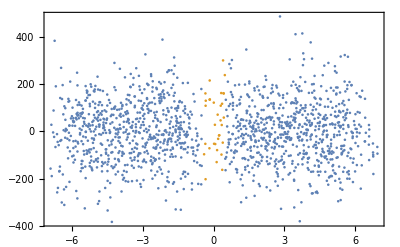

```mathematica
ListPlot[{outsidex[[All,{1,2}]],insidex[[All,{1,2}]]},PlotRange->All,Frame->True,Axes->None]
```

```mathematica
tbin=0.1;
ttmax=Ceiling[Max[-Min[outsidex[[All,1]]],Max[outsidex[[All,1]]]],tbin]
ttmin=-ttmax;
datain=Sort[Join[insidex,outsidex]];
j=0;Label[jloop];j=j+1;tab=Select[datain,ttmin+(j-1)tbin<#[[1]]<ttmin+j tbin&];Subscript[α, j]={ttmin+(j-0.5)tbin,Mean[tab[[All,2]]],StandardDeviation[tab[[All,2]]]/(√(Length[tab]-1))};If[ttmin+j tbin<ttmax,Goto[jloop]];
binned=Table[Subscript[α, jj],{jj,1,j}];
binned=Select[binned,NumberQ[#[[2]]]&&NumberQ[#[[3]]]&];
```

7.

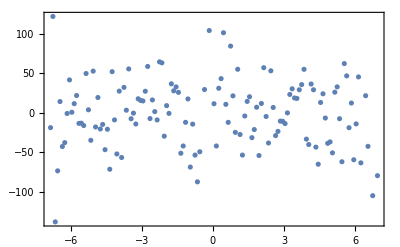

```mathematica
ListPlot[binned[[All,{1,2}]],PlotRange->All,Frame->True,Axes->None]
```

```mathematica
<<ErrorBarPlots`
fn[δ_,t14_,t23_,t_]:=Piecewise[{{0,Abs[t]>0.5t14},{-δ,Abs[t]<0.5t23},{(2 (1+ δ))/(t14- t23)t-((t23+ t14 δ)/(t14-t23)),0.5t23<t<0.5t14},{-(2 (1+ δ))/(t14- t23)t-((t23+ t14 δ)/(t14-t23)),-0.5t14<t<-0.5t23}}];
fn[δ_,w_,t_]:=Piecewise[{{0,Abs[t]>0.5 w},{-δ,Abs[t]<0.5w}}];
xrange2={-2.5,2.5};
yrange2={-200,200};
test1=Select[insidex,xrange2[[1]]<#[[1]]<xrange2[[2]]&&yrange2[[1]]<#[[2]]<yrange2[[2]]&];
test2=Select[outsidex,xrange2[[1]]<#[[1]]<xrange2[[2]]&&yrange2[[1]]<#[[2]]<yrange2[[2]]&];
δbest=bestdip;
truefold=Show[ListPlot[{test1,test2},PlotStyle->{Directive[Gray,Opacity[0.66]],Directive[Gray,Opacity[0.66]]},PlotRange->{xrange2,yrange2},Frame->True,ImageSize->Large,AspectRatio->0.6,Axes->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},FrameLabel->{"time [transit durations]","relative intensity [ppm]"}],ListPlot[binned[[All,{1,2}]],PlotStyle->Black,PlotMarkers->"•"],ErrorListPlot[binned[[All,{1,2,3}]],PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing,Plot[fn[δbest*10^6,1,t],{t,-2.5,2.5},Exclusions->None,PlotStyle->Directive[ColorData["CherryTones"][0.4],Thickness[0.006]]]]
truefold2=Show[ListPlot[binned[[All,{1,2}]],PlotStyle->Black,PlotMarkers->"•",PlotRange->{xrange2,yrange2},Frame->True,ImageSize->Large,AspectRatio->0.6,Axes->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},FrameLabel->{"time [transit durations]","relative intensity [ppm]"}],ErrorListPlot[binned[[All,{1,2,3}]],PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing,Plot[fn[δbest*10^6,1,t],{t,-2.5,2.5},Exclusions->None,PlotStyle->Directive[ColorData["CherryTones"][0.4],Thickness[0.006]]]]
Export[StringJoin[thisfolder,"fold.pdf"],truefold2];
```

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[binned[[All,{1,2}]],PlotStyle->Black,PlotMarkers->"•",PlotRange->{xrange2,yrange2},Frame->None,Axes->None,ImageSize->Large,AspectRatio->0.75,Axes->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},FrameLabel->{"time [transit durations]","relative intensity [ppm]"}],ErrorListPlot[binned[[All,{1,2,3}]],PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing,Plot[fn[δbest*10^6,1,t],{t,-2.5,2.5},Exclusions->None,PlotStyle->Directive[ColorData["CherryTones"][0.4],Thickness[0.006]]]]
```

-Graphics-